### Figures for oriented areas (squares and parallelograms)

```mathematica
ClearAll[o, e1, e2, bold, sz, fs, tsub, midpoint, midtext, shift, sep, p1]
o = {0,0};
e2 = {0,1};
e1 = {1,0};
bold = Style[ #, Bold] &;
sz = 14;
fs = Style[ #, FontSize-> sz] &;
tsub[t_,s_] := Subscript[bold[t]// fs,s];
midpoint[p_] := (p[[1]] + p[[2]])/2 ;
midtext[p_, sh_,text_] := Text[text,midpoint[p] + sh]

shift = -0.06;
sep = 1.5 e1;


ClearAll[parallelogram]

parallelogram[v1_,v2_,ori_,l1_,l2_, c1_, c2_, orientation_]:= Module[{m,r},
m = midpoint[{v1,v2}];
r= Min[
Norm[0.7 (m-v1/2)],
Norm[0.7 (m-v2/2)]];
{Thick,c1,
Arrowheads[0.05],Arrow[{{ori,ori+v1},{ori+v1,ori+v1+v2},{ori+v1+v2,ori+v2},{ori+v2,ori}}],
Black,
midtext[{ori,ori+v1},-shift v2,l1],
midtext[{ori+v1,ori+v1+v2},shift v1,l2],
c2,
Circle[
m + ori,
r,
{0,2 Pi 0.9}],
Arrow[{m+ ori +r e2 -orientation shift e1/2,m+ori +r e2+orientation shift e1/2}]
}];
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/GAelectrodynamics" ]
```

/Users/pjoot/project/figures/GAelectrodynamics

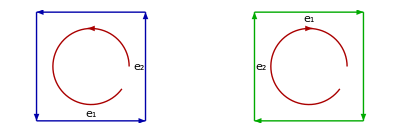

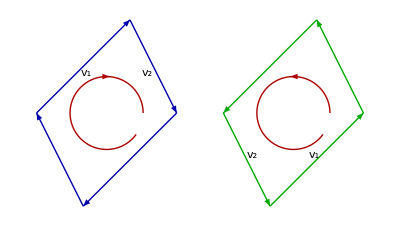

```mathematica
p1 = Graphics[ 
Flatten[
{
parallelogram[e1, e2, o, tsub[e,1], tsub[e,2], Blue//Darker, Red // Darker,1],
parallelogram[e2,e1, 2e1, tsub[e,2], tsub[e,1], Green//Darker, Red // Darker,-1]
}
,1
]]

p2 = Graphics[ 
Flatten[
{
parallelogram[e1+e2, e1/2-e2, o,  tsub[v,1], tsub[v,2], Blue//Darker, Red // Darker,-1],
parallelogram[e1/2-e2,e1+e2, 2e1, tsub[v,2], tsub[v,1], Green//Darker, Red // Darker,1]
}
,1
]]
```

```mathematica
peeters`exportForLatex["orientedAreasFig1", p1]
peeters`exportForLatex["orientedParallelogramFig1", p2]
```

{orientedAreasFig1.eps,orientedAreasFig1pn.png}

{orientedParallelogramFig1.eps,orientedParallelogramFig1pn.png}

### Figures for 90 degree rotations.